# Minimal Simulation of an FPGA for Research in Evolvable Hardware

#### Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fitness[e_,n_,t_]:=
Module[
{allevol,allfit,allparams,bestparams,bestfit,bestindex},
allevol={};
allfit={};
allparams={};
bestparams={};
bestfit  = {};
bestindex={};
For[i=0, i<n, i++,
evol = Transpose[Import[StringJoin[e,"/",ToString[i], "/evol.dat"]]][[2]];
allevol=Append[allevol,evol];
fit=Last[evol];
allfit=Append[allfit,fit];
param = Flatten[Import[StringJoin[e,"/",ToString[i], "/best.gen.dat"]]];
allparams = Append[allparams,param];
If[fit>t ,
bestfit = Append[bestfit,fit];
bestindex=Append[bestindex,i];
bestparams = Append[bestparams,param];
];
];
{bestindex,bestfit,allevol,allfit,bestparams}
]
```

#### Task #1: All board fast-oscillation

```mathematica
n= 100;
t = 0.99;
```

```mathematica
{bestindex,bestfit,allevol,allfit,bestparams} = fitness["E1",n,t];
```

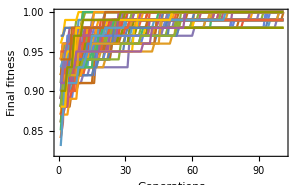

```mathematica
ListLinePlot[allevol,ImageSize->300,PlotRange->All,Frame->True,FrameLabel->{"Generations","Final fitness"}]
```

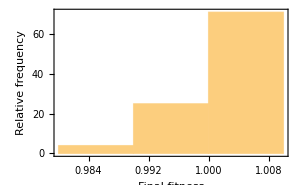

```mathematica
Histogram[allfit,8,PlotRange->All,Frame->True,FrameLabel->{"Final fitness","Relative frequency"},ImageSize->300]
```

#### Task #2: Slow oscillation in a single block